```mathematica
mass ={1.6*10^(-27),
1.7*10^(-27),
2.0*10^(-26),
1.0*10^(-15),
2.7*10^(-14),
6.2*10^(1),
1.8*10^(5),
7.3*10^(22),
5.9*10^(24),
1.9*10^(30),
2.0*10^(30),
2.9*10^(42)};

size={8.4*10^(-16),
1.2*10^(-10),
1.7*10^(-10),
1.1*10^(-6),
3.8*10^(-6),
1.6*10^(1),
2.0*10^(1),
1.7*10^(6),
6.4*10^(6),
7.0*10^(8),
1.4*10^(14),
5.0*10^(20)};
```

```mathematica
compton =Map[10^(-42)/#&,mass]
```

{6.25×10^-16,5.88235×10^-16,5.×10^-17,1.×10^-27,3.7037×10^-29,1.6129×10^-44,5.55556×10^-48,1.36986×10^-65,1.69492×10^-67,5.26316×10^-73,5.×10^-73,3.44828×10^-85}

```mathematica
masses
```

{3.08149×10^-6,5.99624×10^-7,1.49012×10^-8,1.,9.13918×10^-7,6.2,18.8957,9.84244×10^18,3.16554×10^18,2.30467×10^8,1.07374×10^9,2.63461×10^19}

```mathematica
0.243*10^-10=
```

2.43×10^-11

```mathematica
10^-42/(1.4*10^-1)
```

7.14286×10^-42

```mathematica
zipf[m_,z_,c_]:=Labeled[
```

```mathematica
pairedvals=Transpose[{size,compton}];
```

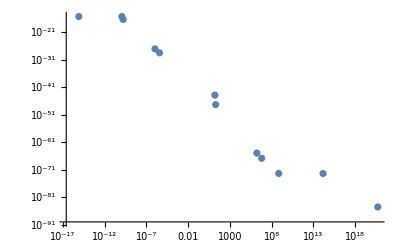

```mathematica
sizevscompton=ListLogLogPlot[pairedvals]
```

```mathematica
fit=LinearModelFit[Log@pairedvals,x,x];
%//Normal
```

-100.485-2.30855 x

```mathematica
fit
```

FittedModel[-100.485-2.30855 x]

```mathematica
LogLogPlot[Normal@fit,{x,10^-16,10^20},Epilog->{PointSize@.02,Point@pairedvals}]
```

-Graphics-